```mathematica
g[s_,n_]:=N[1/(1-2^(1-s))∑_(k=0)^n 1/2^(k+1)∑_(i=0)^k (-1)^i Binomial[k,i] (i+1)^-s]
```

```mathematica
zerig[x_,n_]:= g[0.5+ x I,n]
```

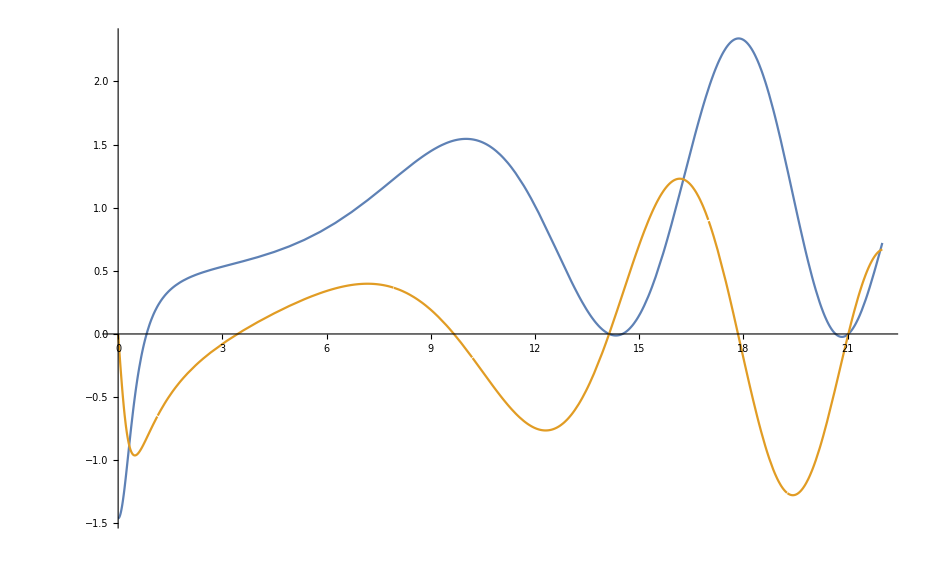

```mathematica
Plot[{Re[zerig[x,40]],Im[zerig[x,40]]},{x,0,22}]
```

```mathematica
N[ZetaZero[2]]
```

0.5+21.022 ⅈ

```mathematica
h[s_,n_]:=N[1/(1-2^(1-s))∑_(k=0)^n 1/2^(k+1)∑_(i=0)^k (-1)^i Binomial[k,i] (i+1)^-s]
```

```mathematica
h[-9,9]
```

-0.00757576

```mathematica
r[s_,k_]:=∑_(i=0)^k (-1)^i Binomial[k,i] (i+1)^s
```

```mathematica
r[5,6]
```

0

```mathematica
p[s_]:=3s^5+4s^4+7s^3-6s^2-5s+10
```

```mathematica
r[j_]:=∑_(i=0)^j (-1)^i Binomial[j,i] p[i]
```

```mathematica
r[6]
```

0

```mathematica
r1[j_]:= ∑_(i=0)^j (-1)^i Binomial[j,i] (2i^2+3i+1)
```

```mathematica
r2[j_]:= 1-j*(6)+j*(j-1)/2 *(15)
```

```mathematica
r2[0]=1
r2[1]=1-6=-5
r2[2]=1-2*6+15=4
r2[3]= 1-3*6+3*15-28 = 0
r2[4]= 1-4*6+6*15-4*28+45= 0
```